```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
```

Data

```mathematica
SetOptions[{Plot},PlotRange->All,Frame->True,ImageSize->300,PlotStyle->{RGBColor[0,0,1]}];SetOptions[{ListPlot},Frame->True,ImageSize->300,PlotStyle->{Hue[1],PointSize[0.02]}];
POCdat=ReadList["YAM_POC.dat",Number,RecordLists->True];
Pordat=ReadList["YAM_Poro.dat",Number,RecordLists->True];
DICpwdat=ReadList["ESYHVD22_DIC.dat",Number,RecordLists->True];
SO4pwdat=ReadList["ESYHVD22_SO4.dat",Number,RecordLists->True];
CH4pwdat=ReadList["ESYHVD22_CH4_v2.dat",Number,RecordLists->True];
Capwdat=ReadList["dummy_Ca.dat",Number,RecordLists->True];
Mgpwdat=ReadList["dummy_Mg.dat",Number,RecordLists->True];
NH4pwdat=ReadList["ESYHVD22_NH4.dat",Number,RecordLists->True];
NO3pwdat=ReadList["ESYHVD22_NO3.dat",Number,RecordLists->True];
OSDpwdat=ReadList["ESYHVD22_OSD.dat",Number,RecordLists->True];
TApwdat=ReadList["ESYHVD22_TA.dat",Number,RecordLists->True];
PO4pwdat=ReadList["ESYHVD22_PO4_v2.dat",Number,RecordLists->True];
Fe2pwdat=ReadList["ESYHVD22_Fe2_v2.dat",Number,RecordLists->True];
HSpwdat=ReadList["ESYHVD22_HS.dat",Number,RecordLists->True];
O2pwdat=ReadList["ESYHVD22_O2_dummy.dat",Number,RecordLists->True];
```

Dissolved and solid species considered in the model

```mathematica
"Dissolved species considered in the model (concentrations in µmol/cm3 = mM)";dspecies={SO4,CH4,DIC,Ca,NH4, PO4,Mg,TA,OSD,Fe2, TH2S, NO3, O2};
"Dissolved species with zero gradient condition at lower boundary";dspecieszg={CH4,DIC,Ca,NH4, Mg,PO4,TA,OSD,Fe2, TH2S, SO4, NO3, O2};
"Dissolved species with non-zero gradient condition at lower boundary";dspeciesnzg={};
"Dissolved species with constant concentration condition at lower boundary";dspeciescc={};
```

Parameter values

```mathematica
"Length of the model column in cm";L:=30;
"Porosity at sediment-water interface";P0=0.81;
"Porosity after compaction";Pf=0.81;
"Parameter for exponential decrease in porosity with depth in 1/cm";px=0.1;
"Burial velocity of solids after compaction in cm/yr";uf=(0.198+0.168+0.235)/3(*0.1/(1-Pf)/2.65*);
"Intergranular upward fluid flow velocity at sediment surface in cm/yr";v0=0;
"Density of dry solids in g/cm3";ds=2.65;
"Bioturbation coefficient at sediment-water interface in cm2/yr (Boudreau 1997: 15.7*uf^0.69) (a very small value for no bioturbation)";DBio0=10^-10;
"Depth of bioturbated zone in cm";xBio=5;
"Bio-irrigation coefficient at x=0 in 1/yr";α0=10(*1.0*);
"Depth of bio-irrigated zone in cm";xBI=10;
"Non-local mixing coefficient induced by filamenteous bacteria at x=0 in 1/yr";αb0=0.0;
"Depth of non-local mixing induced by filamenteous bacteria in cm";xBIB=15.;
"Atomic weight of C";AWC=12;
"Atomic weight of Fe";AW[FeHR]=AW[FeS2]=55.8;
"ratio of Fe:P in depsoited FeHR";                                                                                            εallHR=25;
"ratio of Fe:P in FeHR aged to FeMR";                                                                                     εage=40 ;
"ratio of Fe:P in authigenic iron oxides FeP-A";                                                           εaut=10 ;
"ratio of Fe:P in deposited FeHR";                                                                                            εallHR=25;
"ratio of Fe:P in deposited FeMR";                                                                                            εallMR=0;
"Bottom water temperature in °C";Temp=12;
"Salinity in PSU";Sal=30;
"Molar N:C ratio during POM degradation";rNC=16/106;
"Atomic P-C remineralization ratio in mol P (mol C)–1";rPC=1/106;
"Pressure at the top of the sediment column in bar";Press=1.013;
"Seconds per year";syr=60*60*24*365.25;
```

Parameter values calculated from input parameters

```mathematica
"Simulation time in yr";tmax=5*L/uf;
"Burial velocity of inert solids at sediment-water interface in cm/yr";u0=uf*(1-Pf)/(1-P0);
"Mass accumulation rate of inert particles in g/cm2/yr";MAR=ds*(1-P0)*u0;
"Dynamic viscosity of water in centipoise (Kukulka et al. 1987 after Boudreau 1997)";μW=1.7910-Temp*(6.144*10^-2-Temp*(1.4510*10^-3-Temp*1.6826*10^-5))-1.5290*10^-4*Press+8.3885*10^-8*Press*Press+2.4727*10^-3*Sal+(6.0574*10^-6*Press-2.6760*10^-9*Press*Press)*Temp+(Temp*(4.8429*10^-5-Temp*(4.7172*10^-6-Temp*7.5986*10^-8)))*Sal;

"Molecular diffusion coefficient for DIC in cm2/yr(Burdige ref.1 Table 3)";DDIC=(5.06+0.275*Temp)*(10^-6)*syr;
"Molecular diffusion coefficient for SO4 in cm2/yr(Burdige ref.1 Table 3)";DSO4=(4.88+0.232*Temp)*(10^-6)*syr;
"Molecular diffusion coefficient for SO4 in cm2/yr(Burdige ref.1 Table 3)";DOSD=(4.88+0.232*Temp)*(10^-6)*syr;
"Molecular diffusion coefficient for methane in cm2/yr (Burdige ref.1 Table 3) "; DCH4=syr*4.72*10^-9*(Temp+273.15)/(μW*0.01*37.7^0.6);
"Molecular diffusion coefficient for Ca in cm2/yr(Burdige ref.1 Table 3)";DCa=(3.6+0.179*Temp)*10^-6*syr;
"Molecular diffusion coefficient for Mg in cm2/yr";DMg=(3.43+0.144*Temp)*10^-6*syr;
"Molecular diffusion coefficient for NH4 in cm2/yr";DNH4=(9.5+0.413*Temp)*(10^-6)*syr;
"Molecular diffusion coefficient for PO4 in cm2/yr";DPO4=(3.26+0.177*Temp)*(10^-6)*syr ;
"Molecular diffusion coefficient for TA(HCO3) in cm2/yr";DTA=DDIC;
"Molecular diffusion coefficient for Fe2+ in cm2/yr";DFe2=99+4.4*Temp;
"Moleculare diffusion coefficient for H2S in cm2/yr (Oelkers et al. 1991 after Boudreau 1997)"; DH2S=syr*4.72*10^-9*(Temp+273.15)/(μW*0.01*35.2^0.6);
"Molecular diffusion coefficient for HS in cm2/yr";DHS=(10.4+0.273*Temp)*(10^-6)*syr;
"Molecular diffusion coefficient for THS in cm2/yr";DTH2S=(DH2S+DHS)/2;
"Molecular diffusion coefficient for O2 in cm2/yr (Oelkers et al. 1991 after Boudreau 1997)"; 
DO2=syr*4.72*10^-9*(Temp+273.15)/(μW*0.01*27.9^0.6);
"Molecular diffusion coefficient for NO3 in cm2/yr";DNO3=(9.50+0.388*Temp)*(10^-6)*syr;


(*Print["DDIC = ",DDIC," cm^2/yr"]
Print["DSO4 = ",DSO4," cm^2/yr"]
Print["DCH4 = ",DCH4," cm^2/yr"]
Print["DCa = ",DCa," cm^2/yr"]
Print["DMg = ",DMg," cm^2/yr"]
Print["DNH4 = ",DNH4," cm^2/yr"]
Print["DPO4 = ",DPO4," cm^2/yr"]
Print["DTA = ",DTA," cm^2/yr"]
Print["DFe2 = ",DFe2," cm^2/yr"]
Print["DH2S = ",DH2S," cm^2/yr"]
Print["DHS = ",DHS," cm^2/yr"]
Print["DTH2S = ",DTH2S," cm^2/yr"]*)
```

```mathematica
748.7520798668886
```

748.752

Depth-dependent functions

```mathematica
"Sediment porosity as a function of depth";Poro[x_]:=Pf+(P0-Pf)*Exp[-px*x];(*0.78+0.07*Exp[-0.174*x]+0.15*Exp[-0.006*x]*);
"Tortuosity^2 according in Boudreau (1997)";to[x_]:=1-2*Log[Poro[x]];
"Burial velocity of solids with steady state compaction in cm/yr";us[x_]:=(1-Pf)*uf/(1-Poro[x]); 
"Burial velocity of pore water with steady state compaction and upward fluid flow in cm/yr";upw[x_]:=Pf*uf/Poro[x]-v0*P0/Poro[x];
"Bioturbation coefficient in sediments in cm2/yr";DBio[x_]:=DBio0*Exp[-x^2/(2*xBio^2)];
"Bio-irrigation coefficient in sediments in cm2/yr";α[x_]:=α0*Exp[-x^2/(2*xBI^2)];
"Bio-irrigation coefficient induced by filamenteous bacteria in 1/yr";αb[x_]:=αb0*Exp[-x^2/(2*xBIB^2)];
"Diffusion coefficient in sediment for DIC in cm2/yr";Ds[DIC][x_]:=DDIC/to[x]+DBio[x];
"Diffusion coefficient in sediment for Mg in cm2/yr";Ds[Mg][x_]:=DMg/to[x]+DBio[x];
"Diffusion coefficient in sediment for SO4 in cm2/yr";Ds[SO4][x_]:=10*DSO4/to[x]+DBio[x];
"Diffusion coefficient in sediment for methane in cm2/yr"; Ds[CH4][x_]:=DCH4/to[x]+DBio[x];
"Diffusion coefficient in sediment for NH4 in cm2/yr"; Ds[NH4][x_]:=DNH4/to[x]+DBio[x];
"Diffusion coefficient in sediment for Ca in cm2/yr"; Ds[Ca][x_]:=DCa/to[x]+DBio[x];
"Diffusion coefficient in sediment for PO4 in cm2/yr"; Ds[PO4][x_]:=DPO4/to[x]+DBio[x];
"Diffusion coefficient in sediment for TA in cm2/yr";Ds[TA][x_]:=DTA/to[x]+DBio[x];
"Diffusion coefficient in sediment for OSD in cm2/yr";Ds[OSD][x_]:=DOSD/to[x]+DBio[x];
"Diffusion coefficient in sediment for Fe2 in cm2/yr"; Ds[Fe2][x_]:=DFe2/to[x]+DBio[x];
"Diffusion coefficient in sediment for TH2S in cm2/yr";Ds[TH2S][x_]:=DTH2S/to[x]+DBio[x];
"Diffusion coefficient in sediment for O2 in cm2/yr"; Ds[O2][x_]:=DO2/to[x]+DBio[x];
"Diffusion coefficient in sediment for NO3 in cm2/yr";Ds[NO3][x_]:=DNO3/to[x]+DBio[x];
```

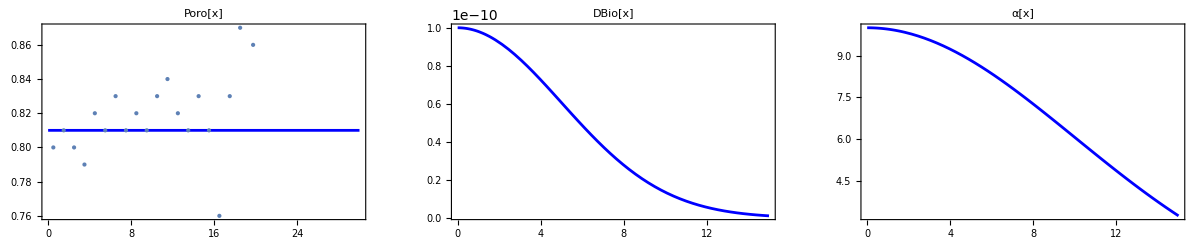

```mathematica
GraphicsGrid[{{Show[Plot[Poro[x],{x,0,L},PlotRange->All,PlotPoints->100,PlotLabel->"Poro[x]"],ListPlot[Pordat,PlotStyle->PointSize->Large]],Plot[DBio[x],{x,0,15},PlotRange->All,PlotLabel->"DBio[x]"],Plot[α[x],{x,0,15},PlotRange->All,PlotLabel->"α[x]"]}}]
```

Fit function for Ca data

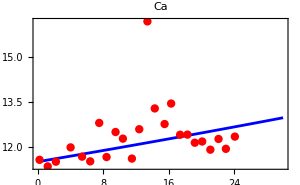

```mathematica
Caintx[x_]:=11.5*Exp[0.004*x]
Show[{Plot[Caintx[x],{x,0,L},DisplayFunction->Identity],ListPlot[Capwdat,DisplayFunction->Identity]},DisplayFunction->$DisplayFunction,PlotLabel->"Ca"]
```

Fit function for Mg data

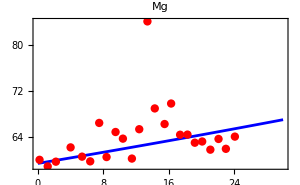

```mathematica
Mgintx[x_]:=59.5*Exp[0.004*x]
Show[{Plot[Mgintx[x],{x,0,L},DisplayFunction->Identity],ListPlot[Mgpwdat,DisplayFunction->Identity]},DisplayFunction->$DisplayFunction,PlotLabel->"Mg"]
```

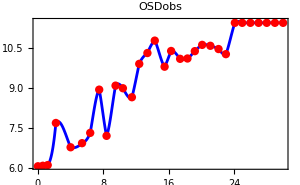

```mathematica
OSDobsdata={{0,6.0809},{0.6,6.10},{1.2,6.125488},{2.2,7.6935},{4,6.7889},{5.4,6.9419},{6.4,7.32487},{7.5,8.93618},{8.4,7.21483},(*{300,4.8922},{330,5.8922},{340,5.9922},*){9.5,9.08509},{10.4,8.98828},{11.5,8.6532},{12.4,9.8963},{13.4,10.3},(*{13.4,13.10621},*){14.3,10.7624},{15.5,9.7907},{16.3,10.3763},{17.4,10.0840},{18.3,10.0966},{19.2,10.3699},{20.1,10.6039},{21.1,10.56969},{22.1,10.4488},{23,10.25856},{24.1,11.42535},{25,11.42535},{26,11.42535},{27,11.42535},{28,11.42535},{29,11.42535},{L,11.42535}};
(*FG1upb=Interpolation[G1data,InterpolationOrder->1];*)
OSDobsdati=Table[{findi[OSDobsdata[[iter,1]]],OSDobsdata[[iter,2]]},{iter,1,Length[OSDobsdata]}];
OSDobsintx[x_]:=Interpolation[OSDobsdata, InterpolationOrder->3][x];

Show[{Plot[OSDobsintx[x],{x,0,L},DisplayFunction->Identity],ListPlot[OSDobsdata,DisplayFunction->Identity]},DisplayFunction->$DisplayFunction,PlotLabel->"OSDobs"]

KOSDobs=1.5;
ROSD[x_,t_]:=KOSDobs*(OSDobsintx[x]-(OSD[x,t]));
```

```mathematica
(*OSDobint[x_]:=Interpolation[{{0,6.0809},{0.6,6.10},{1.2,6.125488},{2.2,7.6935},{4,6.7889},{5.4,6.9419},{6.4,7.32487},{7.5,8.93618},{8.4,7.21483},(*{300,4.8922},{330,5.8922},{340,5.9922},*){9.5,9.08509},{10.4,8.98828},{11.5,8.6532},{12.4,9.8963},{13.4,13.10621},{14.3,10.7624},{15.5,9.7907},{16.3,10.3763},{17.4,10.0840},{18.3,10.0966},{19.2,10.3699},{20.1,10.6039},{21.1,10.56969},{22.1,10.4488},{23,10.25856},{24.1,11.42535},{25,11.42535},{26,11.42535},{27,11.42535},{28,11.42535},{29,11.42535},{L,11.42535}},InterpolationOrder->1][x];
OSDobsintx[x_]:=OSDobint[x]
Show[{Plot[OSDobsintx[x],{x,0,L},DisplayFunction->Identity],ListPlot[OSDobsdata,DisplayFunction->Identity]},DisplayFunction->$DisplayFunction,PlotLabel->"OSDobs"]
KOSDobs=5;
ROSD[x_,t_]:=KOSDobs*(OSDobsinti[x]-(OSD[x,t]));*)
```

```mathematica
(*SO4dati=Table[{findi[SO4data[[iter,1]]],SO4data[[iter,2]]},{iter,1,Length[SO4data]}];*)
```

```mathematica
(*SO4int[i_]:=Interpolation[SO4data, InterpolationOrder->3][xvar[i]];
SO4intx[x_]:=Interpolation[SO4data, InterpolationOrder->3][x];
Show[{Plot[SO4int[i],{i,0,n},DisplayFunction->Identity],ListPlot[SO4dati,DisplayFunction->Identity]},DisplayFunction->$DisplayFunction,PlotLabel->"SO4"];
Show[{Plot[SO4intx[x],{x,0,L},DisplayFunction->Identity],ListPlot[SO4data,DisplayFunction->Identity]},DisplayFunction->$DisplayFunction,PlotLabel->"SO4"]
RSO4[i_][t_]:=KSR*(SO4int[i]/1000-sp[8][i][t]);*)
```

Definition of grid

```mathematica
"Uneven model grid with high resolution at upper boundary";grid=Table[x^2,{x,0,L^(1/2),0.04}];
"Length of the model column in cm";L=Last[grid]
"Number of cells";Length[grid]
```

29.5936

137

Rate constants

```mathematica
"Kinetic constant for the anaerobic oxidation of methane in 1/(yr)(Burdige ref.1 Table 4)";kAOM=0.5;
"Monod constant for sulfate reduction in µmol/cm3 (Burdige ref.1 Table 2; Km)";kSulf=0.0005*10^3;
"AOM half saturation constant in µmol/cm3 (Burdige ref.1 Table 2)"; Ka=0.001*10^3;
"Rate constant for POC degradation in 1/yr (Burdige ref.1 Table 4)";
k=0.007;
"Kinetic constant for anaerobic CH4 oxidation as function of depth in cm3/µmol/yr";kSO4CH4=0.2(*200*);
"Rate constant for reduction of FeHR by sulfide (cm3/µmol/yr)"; kFeHR=10(*100.00*);
"Monod constant for iron reduction in gFe/g_dry_solid";KFe3POC=0.0001(*0.0001*);
"Rate Constant for FeS2 precipitation with Fe2 + H2S  cm.b3/µmol/yr"; kFeS2p3=1;
"Atomic P-C remineralization ratio from Pei's paper"
rPCr1=5/106;
"Kinetic constant for anaerobic TH2S oxidation by NO3 yr-1";kNO3TH2S=180(*000*);
```

Atomic P-C remineralization ratio from Pei's paper

Depth and time-dependent functions (kinetic rate laws)

```mathematica
"Rate of POC degradation in wt/yr (Burdige ref.1 Table 4)";

(*POCdegr[x_,t_]:=k*POC[x,t];*)
POCdegr[x_,t_]:=0.5*ROSD[x,t]*(kSulf+SO4[x,t])/SO4[x,t]*2/(ds*(1-Poro[x])*10^6/(Poro[x]*AWC));

"Factor relating POC-conc. in g/g to DIC conc. in µmol/cm3";rC[x_]:=ds*(1-Poro[x])*10^6/(Poro[x]*AWC);
"Factor relating Fe in g/g to Fe2 conc. in µmol/cm3";rFe[x_]:=ds*(1-Poro[x])/Poro[x]/AW[FeHR]*10^6;
"Factor relating P in g/g to PO4 conc. in µmol/cm3";rP[x_]:=ds*(1-Poro[x])/Poro[x]/AW[P]*10^6;

"Rate of dissolved carbon production via POC degradation (HCO3+CH4) in µmol C/cm3PW/yr";
RDICPOC[x_,t_]:=POCdegr[x,t]*ds*(1-Poro[x])*10^6/(Poro[x]*AWC);

"Rate of carbonate dissolution CaCO3 = Ca + CO3 in µmol Ca/cm3/yr; ACP(z)=Rmax*Exp[-0.5*((zcp - z)/scp)^2](Burdige ref.1 Eq. 10 )";
RCa[x_,t_]:=0;
"Rate of carbonate dissolution MgCO3 = Mg + CO3 in mmol Mg/cm3/yr";
RMg[x_,t_]:=0;
"Sulfate reduction rate without pyrite formation in µmol S/cm3/yr
C(H2O) + 1/2 SO42- = 1/2 HS- + HCO3- + 1/2 H+ (Burdige ref.2 Eq. A7==> Km=kSulf; ζ=1/rC[i]; POCdegr[i][t]=kiGi)";
RSR[x_,t_]:=0.5*SO4[x,t]/(kSulf+SO4[x,t])*RDICPOC[x,t];

"Rate of methane generation via anaerobic degradation of POC in µmol CH4/cm3/yr (Burdige ref.2 Eq. A1a)";
RMC[x_,t_]:=0.5*kSulf/(kSulf+SO4[x,t])*RDICPOC[x,t];   

"Rate of DIC left after methane production in the methanogenesis zone in µmol DIC/cm3/yr (Burdige ref.2 Eq. A4)";

"Rate of anaerobic methane oxidation (Burdige ref.2 Eq. A1b)";
RAOM[x_,t_]:=(*ROSD[x,t]-RSR[x,t]*)kAOM*SO4[x,t]/(Ka+SO4[x,t])*CH4[x,t];
"Rate of PO4 release via POM degradation in µmol P/cm3PW/yr, POM + rPC H+ → rPC PO4"; 
RPO4POC[x_,t_]:=rPCr1*POCdegr[x,t]*rC[x];

"Rate of POC degradation via iron reduction in µmol Fe/cm3PW/yr, POC + 4Fe(OH)3 + 7H+ -> HCO3- + 10H2O + 4Fe2+";
RFe3POC[x_,t_]:=1.00*4*RDICPOC[x,t]*(FeHR[x,t]/(KFe3POC+FeHR[x,t]));
"Rate of anaerobic CH4 oxidation in µmol CH4/cm3PW/yr, CH4 + SO42- +2H+ → H2S + CO2 + 2H2O";
RSO4CH4[x_,t_]:=1.00*kSO4CH4*SO4[x,t]*CH4[x,t];
"Rate of FeS2 precipitation in µmol Fe/cm3/yr, Fe2+ + 2H2S -> FeS2 + 2H+ + H2";
RFeS2p3[x_,t_]:=1.00*kFeS2p3*TH2S[x,t]*Fe2[x,t];
"Rate of FeHR dissolution by sulfide µmol Fe/cm3/yr, Fe(OH)3 + H2S +H+ → 0.5*FeS2 + 0.5Fe2+ + 3H2O";
RFeHRred[x_,t_]:=1.00*kFeHR*TH2S[x,t]*FeHR[x,t]*rFe[x];
"Rate of anaerobic TH2S oxidation by NO3 µmol N/cm3PW/yr, H2S + NO3- + H2O → SO42- + NH4+ "; 
RNO3TH2S[x_,t_]:=1.00*kNO3TH2S*TH2S[x,t]*NO3[x,t]
```

Rate terms and reaction network for dissolved species

```mathematica
"Ca rates in µmol Ca/(cm3 PW yr)";  rate[Ca][x_,t_]:=-RCa[x,t];
"SO4 rates in µmol SO4/(cm3 PW yr)"; rate[SO4][x_,t_]:=(*-ROSD[x,t]*)-RSR[x,t]-RAOM[x,t]+RNO3TH2S[x,t];
"CH4 rates in µmol CH4/(cm3 PW yr)";rate[CH4][x_,t_]:=RMC[x,t]-RAOM[x,t];
"DIC rates in µmol DIC/(cm3 PW yr)";  rate[DIC][x_,t_]:=-RCa[x,t]-RMg[x,t]+RDICPOC[x,t]-RMC[x,t]+RAOM[x,t];
"Mg rates in µmol Mg/(cm3 PW yr)";  rate[Mg][x_,t_]:=-RMg[x,t];
"NH4 rates in µmol NH4/(cm3 PW yr)";rate[NH4][x_,t_]:=RDICPOC[x,t]*rNC;
"PO4 rates in µmol P/(cm3 PW yr)";rate[PO4][x_,t_]:=RDICPOC[x,t]*rPC;
"TA rates in µEq. TA/(cm3 PW yr)"; rate[TA][x_,t_]:=+rate[NH4][x,t]+2*RSR[x,t]+2*RAOM[x,t]-2*RCa[x,t]-2*RMg[x,t]-rate[PO4][x,t]+RNO3TH2S[x,t];
"OSD rates in OSD(cm3 PW yr)"; rate[OSD][x_,t_]:=ROSD[x,t];
"Fe2 rates in µmol Fe/(cm3 PW yr)";rate[Fe2][x_,t_]:=1.00*(RFe3POC[x,t]-RFeS2p3[x,t]+0.5*RFeHRred[x,t]);
"TH2S rates in µmol S/(cm3 PW yr)";rate[TH2S][x_,t_]:= 1.00 *(+RSR[x,t]+RSO4CH4[x,t]-2*RFeS2p3[x,t]-RFeHRred[x,t]-RNO3TH2S[x,t]);
(*1.00*(+RSO4POC[x,t]-RO2TH2S[x,t]-RNO3TH2S[x,t]-5/8*RNO3TH2Sm[x,t]-(RFeHRred[x,t]+RFeMRred[x,t]+RFePRred[x,t])-RSorg[x,t]+0.25*RSO4H2[x,t])*)
rate[O2][x_,t_]:=0;
rate[NO3][x_,t_]:=-RNO3TH2S[x,t];
```

Rate terms and reaction network for solid species

```mathematica
"Rate of POC in gC/gSed/yr";RPOC[x_,t_]:=POCdegr[x,t];
"FeHR rates in gFe/g_dry_sed/yr"; RFeHR[x_,t_]:=1.00*(-RFe3POC[x,t]-RFeHRred[x,t] )/rFe[x];
"FeS2 rates in gFeS2/g_dry_sed/yr"; 
RFeS2[x_,t_]:=1.00*(RFeS2p3[x,t]+0.5*(RFeHRred[x,t]))/rFe[x];
```

Partial differential equations (PDEs)

```mathematica
"PDE for POC in gC/gS/yr";PDEPOC=D[ds*(1-Poro[x])*POC[x,t],t]==D[ds*(1-Poro[x])*DBio[x]*D[POC[x,t],x],x]-D[ds*(1-Poro[x])*us[x]*POC[x,t],x]-ds*(1-Poro[x])*RPOC[x,t];

"PDE for FeS2 in ?/yr";PDEFeS2=D[ds*(1-Poro[x])*FeS2[x,t],t]==D[ds*(1-Poro[x])*DBio[x]*D[FeS2[x,t],x],x]-D[ds*(1-Poro[x])*us[x]*FeS2[x,t],x]+ds*(1-Poro[x])*RFeS2[x,t];

"PDE for FeHR in ?/yr";PDEFeHR=D[ds*(1-Poro[x])*FeHR[x,t],t]==D[ds*(1-Poro[x])*DBio[x]*D[FeHR[x,t],x],x]-D[ds*(1-Poro[x])*us[x]*FeHR[x,t],x]+ds*(1-Poro[x])*RFeHR[x,t];

"PDE for dissolved species in µmol/cm3PW/yr";PDEdspecies=Table[D[Poro[x]*dspecies[[i]][x,t],t]==D[Poro[x]*Ds[dspecies[[i]]][x]*D[dspecies[[i]][x,t],x],x]-D[Poro[x]*upw[x]*dspecies[[i]][x,t],x]+Poro[x]*α[x]*(BW[dspecies[[i]]]-dspecies[[i]][x,t])+Poro[x]*rate[dspecies[[i]]][x,t],{i,1,Length[dspecies]}];
```

Upper boundary conditions at sediment-water interface

```mathematica
"POC content in gC/gSed(Burdige ref.1 Table 4)";UBPOC=POC[0,t]==10/100;
UBFeS2=FeS2[0,t]==0.1/100;
UBFeHR=FeHR[0,t]==0.1/100;

"Bottom water concentration of dissolved species in mM (=µmol/cm3)";

BW[Ca]=Caintx[0];
BW[SO4]=25;
BW[CH4]=1*10^-20;
BW[DIC]=5.43;
BW[Mg]=Mgintx[0];
BW[NH4]=0.38;
BW[PO4]=0.015(*0.035*)(*0*);
BW[TA]=5.15;
BW[OSD]=0;
BW[Fe2]=0;
BW[TH2S] = 0.3;
BW[O2]=0;
BW[NO3]=0.03;
"Upper boundary condition for dissolved species with constant concentrations";UBdspecies=Table[dspecies[[i]][0,t]==BW[dspecies[[i]]],{i,1,Length[dspecies]}];
```

Lower boundary conditions at x = L

```mathematica
"Zero gradient condition for POC in g/cm2/yr";LBPOC=Derivative[1,0][POC][L,t]==0;
LBFeS2=Derivative[1,0][FeS2][L,t]==0;
LBFeHR=Derivative[1,0][FeHR][L,t]==0;

"Concentration of dissolved species at lower boundary in mM (=µmol/cm3)";LBC[SO4]=21;
LBC[Ca]=Caintx[L];
LBC[CH4]=0;
LBC[DIC]=10;
LBC[Mg]=Mgintx[L];
LBC[NH4]=2.2;
LBC[Fe2]=0;
LBC[TH2S] = 1.4;
LBC[O2]=0;
LBC[NO3] = 0.04;



"Zero gradient or constant concentration condition at lower boundary for dissolved species";
LBdspecies=Flatten[{Table[Derivative[1,0][dspecieszg[[i]]][L,t]==0,{i,1,Length[dspecieszg]}],Table[Derivative[1,0][dspeciesnzg[[i]]][L,t]==LBF[dspeciesnzg[[i]]]/Pf/Ds[dspeciesnzg[[i]]][L],{i,1,Length[dspeciesnzg]}],Table[dspeciescc[[i]][L,t]==LBC[dspeciescc[[i]]],{i,1,Length[dspeciescc]}]}];
```

Initial conditions as calculated from boundary conditions

```mathematica
INIPOC=POC[x,0]==10/100;
INIFeS2=FeS2[x,0]==0.078/100;
INIFeHR=FeHR[x,0]==0.09/100;

INIdspecies=Flatten[{Table[dspecieszg[[i]][x,0]==BW[dspecieszg[[i]]],{i,1,Length[dspecieszg]}],
Table[dspeciesnzg[[i]][x,0]==BW[dspeciesnzg[[i]]]+LBF[dspeciesnzg[[i]]]/Poro[x]/Ds[dspeciesnzg[[i]]][x]*x,{i,1,Length[dspeciesnzg]}],Table[dspeciescc[[i]][x,0]==BW[dspeciescc[[i]]]+(LBC[dspeciescc[[i]]]-BW[dspeciescc[[i]]])/L*x,{i,1,Length[dspeciescc]}]}];
```

Solution of PDE

```mathematica
Timing[solPOC=NDSolve[Flatten[{PDEPOC, PDEFeS2, PDEFeHR, UBPOC,UBFeS2, UBFeHR, LBPOC,LBFeS2, LBFeHR, INIPOC,INIFeS2, INIFeHR, PDEdspecies,UBdspecies,LBdspecies,INIdspecies}],Flatten[{POC,FeHR, FeS2, dspecies}],{x,0,L},{t,0,tmax},MaxSteps->10^6,StepMonitor:>Print[t],Method->{"MethodOfLines", "SpatialDiscretization"->{"TensorProductGrid",   "Coordinates"->grid}(*,Method->{IDA}*)}(*,AccuracyGoal->8,PrecisionGoal->6*)];];
```

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

1.10468×10^-11

2.20936×10^-11

3.31404×10^-11

4.41872×10^-11

5.5234×10^-11

7.73275×10^-11

9.94211×10^-11

1.21515×10^-10

3.42451×10^-10

5.63386×10^-10

7.84322×10^-10

2.99368×10^-9

5.20304×10^-9

7.4124×10^-9

1.07857×10^-8

1.4159×10^-8

1.75323×10^-8

1.92093×10^-8

2.08864×10^-8

2.25634×10^-8

2.34656×10^-8

3.24878×10^-8

4.15099×10^-8

5.0532×10^-8

1.40753×10^-7

2.30975×10^-7

1.13319×10^-6

2.0354×10^-6

0.0000110575

0.0000200797

0.000081542

0.000143004

0.00028879

0.000434576

0.000674621

0.000914665

0.00130303

0.0016914

0.00207977

0.00277281

0.00346585

0.0041589

0.00523935

0.0063198

0.00740025

0.00909106

0.0107819

0.0124727

0.0141635

0.0165145

0.0188655

0.0212165

0.0235675

0.0273616

0.0311557

0.0349498

0.0387439

0.0441185

0.0494931

0.0548677

0.0602423

0.0689749

0.0777076

0.0864402

0.0951729

0.109266

0.12336

0.137454

0.151547

0.171602

0.191657

0.211711

0.231766

0.251821

0.271875

0.29193

0.30844

0.32495

0.34146

0.35797

0.37448

0.390989

0.407499

0.424009

0.443095

0.462182

0.481268

0.500354

0.522135

0.543917

0.565698

0.569098

0.572497

0.575897

0.581623

0.58735

0.602963

0.618577

0.634191

0.670606

0.70702

0.743435

0.779849

0.824525

0.869201

0.913877

0.958553

1.02484

1.09112

1.15741

1.22369

1.31478

1.40586

1.49694

1.58802

1.71568

1.84333

1.97099

2.09864

2.26648

2.43432

2.60215

2.76999

2.93782

3.10566

3.27349

3.44133

3.47252

3.50371

3.5349

3.56608

3.6238

3.68151

3.73923

3.79694

4.05352

4.31009

4.56667

5.04044

5.51422

5.98799

6.46176

8.47708

10.4924

12.5077

19.6543

26.8009

40.4531

54.1054

72.7007

91.2961

115.747

140.198

164.648

202.075

239.502

276.928

351.803

426.679

501.554

576.429

651.304

700.028

748.752

NDSolve::eerr: Warning: scaled local spatial error estimate of 62.3637 at t = 748.752 in the direction of independent variable x is much greater than the prescribed error tolerance. Grid spacing with 137 points may be too large to achieve the desired accuracy or precision. A singularity may have formed or a smaller grid spacing can be specified using the MaxStepSize or MinPoints method options.

Plots of model results at tmax (steady state)

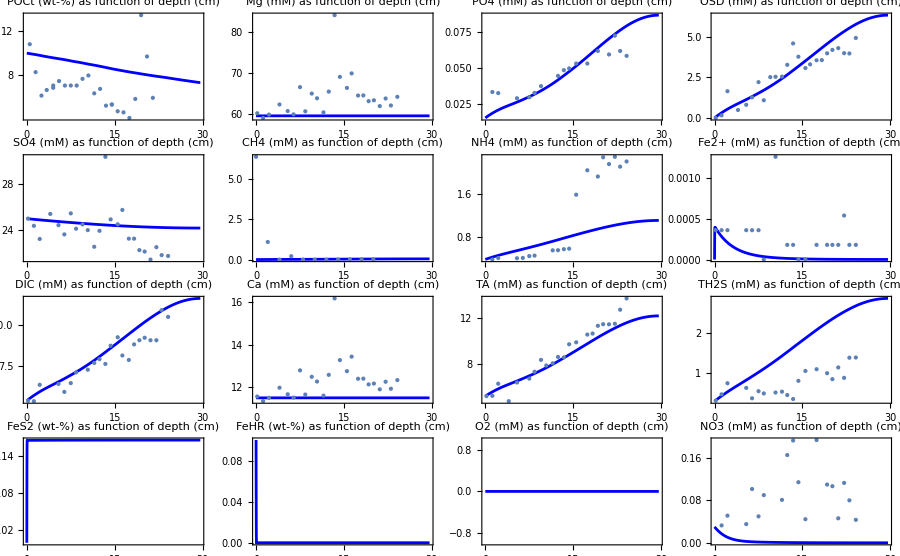

```mathematica
Show[GraphicsGrid[{{Show[Plot[{100*POC[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"POCt (wt-%) as function of depth (cm)"],ListPlot[POCdat,PlotStyle->PointSize->Large]],Show[Plot[{Mg[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"Mg (mM) as function of depth (cm)"],ListPlot[Mgpwdat,PlotStyle->PointSize->Large]],Show[Plot[{PO4[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"PO4 (mM) as function of depth (cm)"],ListPlot[PO4pwdat,PlotStyle->PointSize->Large]],Show[Plot[{OSD[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"OSD (mM) as function of depth (cm)"],ListPlot[OSDpwdat,PlotStyle->PointSize->Large]]},{Show[Plot[{SO4[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"SO4 (mM) as function of depth (cm)"],ListPlot[SO4pwdat,PlotStyle->PointSize->Large]],Show[Plot[{CH4[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"CH4 (mM) as function of depth (cm)"],ListPlot[CH4pwdat,PlotStyle->PointSize->Large]],Show[Plot[{NH4[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"NH4 (mM) as function of depth (cm)"],ListPlot[NH4pwdat,PlotStyle->PointSize->Large]],
Show[Plot[{Fe2[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"Fe2+ (mM) as function of depth (cm)"],ListPlot[Fe2pwdat,PlotStyle->PointSize->Large]]},{Show[Plot[{DIC[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"DIC (mM) as function of depth (cm)"],ListPlot[DICpwdat,PlotStyle->PointSize->Large]],Show[Plot[{Ca[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"Ca (mM) as function of depth (cm)"],ListPlot[Capwdat,PlotStyle->PointSize->Large]],Show[Plot[{TA[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"TA (mM) as function of depth (cm)"],ListPlot[TApwdat,PlotStyle->PointSize->Large]],
Show[Plot[{TH2S[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"TH2S (mM) as function of depth (cm)"],ListPlot[HSpwdat,PlotStyle->PointSize->Large]]},
{Show[Plot[{100*FeS2[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"FeS2 (wt-%) as function of depth (cm)"]],Show[Plot[{100*FeHR[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"FeHR (wt-%) as function of depth (cm)"]],Show[Plot[{O2[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"O2 (mM) as function of depth (cm)"]],
Show[Plot[{NO3[x,tmax]/.solPOC},{x,0,L},PlotRange->All,PlotLabel->"NO3 (mM) as function of depth (cm)"],ListPlot[NO3pwdat,PlotStyle->PointSize->Large]]}}],ImageSize->900]
```

```mathematica
"export calculated model into csv files"

(*modeldata=Table[{x,(First[CH4[x,tmax]/. solPOC]),(First[DIC[x,tmax]/. solPOC]),(First[PO4[x,tmax]/. solPOC]),(First[SO4[x,tmax]/. solPOC]),(First[OSD[x,tmax]/. solPOC]),(First[NH4[x,tmax]/. solPOC]),(First[Fe2[x,tmax]/. solPOC]),(First[TA[x,tmax]/. solPOC]),(First[TH2S[x,tmax]/. solPOC]), First[100*POC[x,tmax]/.solPOC]},{x,0,L,L/100}]; (*Adjust step size as needed*)
Export["C:\\Users\\spit\\OneDrive - ucsc.edu\\PhD\\Elkhorn Slough\\Data\\Raw\\Masterfiles\\model_ESYHVD22_03-14-2025.csv",modeldata,"CSV"]*)
```

export calculated model into csv files

Steady state results and mass balances

```mathematica
{{"Fluxes at tmax in µmol/cm2/yr"},{"","at x=0","at x=L","Bio-Irrigation", "Total through x = 0"},{"POC",FluxPOC0=10^6/AWC*ds*(1-P0)*(u0*POC[0,tmax]-DBio0*Derivative[1,0][POC][0,tmax])/.solPOC[[1]],FluxPOCL=10^6/AWC*ds*(1-Poro[L])*(us[L]*POC[L,tmax]-DBio[L]*Derivative[1,0][POC][L,tmax])/.solPOC[[1]]},
{Table[dspecies[[i]],{i,1,Length[dspecies]}],Table[Flux0[dspecies[[i]]]=Poro[0]*(upw[0]*dspecies[[i]][0,tmax]-Ds[dspecies[[i]]][0]*Derivative[1,0][dspecies[[i]]][0,tmax])/.solPOC[[1]],{i,1,Length[dspecies]}],Table[FluxL[dspecies[[i]]]=Poro[L]*(upw[L]*dspecies[[i]][L,tmax]-Ds[dspecies[[i]]][L]*Derivative[1,0][dspecies[[i]]][L,tmax])/.solPOC[[1]],{i,1,Length[dspecies]}],Table[RateNLM[dspecies[[i]]]=0.00*NIntegrate[Poro[x]*(α[x])*(BW[dspecies[[i]]]-dspecies[[i]][x,tmax])/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}],{i,1,Length[dspecies]}],Table[Flux0tot[dspecies[[i]]]=Flux0[dspecies[[i]]]+RateNLM[dspecies[[i]]],{i,1,Length[dspecies]}]}}//TableForm

{{"Depth-integrated rates at tmax in µmol/cm2/yr"},{"POC degradation (POC) in µmol C/cm2/yr",ratePOC=10^6/AWC*ds*NIntegrate[(1-Poro[x])*RPOC[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},

{"Methanogenesis in µmol CH4/cm2/yr",RateRMC=NIntegrate[Poro[x]*RMC[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"Sulfate Reduction in µmol SO4/cm2/yr",RateRSR=NIntegrate[Poro[x]*RSR[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"Rate of carbonate dissolution in µmol Ca/cm3/yr",RateRCa=NIntegrate[Poro[x]*RCa[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"Rate of carbonate dissolution in µmol Mg/cm3/yr",RateRMg=NIntegrate[Poro[x]*RMg[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"Rate of NH4 release in µmol Mg/cm3/yr",RateRNH4=NIntegrate[Poro[x]*RDICPOC[x,tmax]*rNC/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"Rate of OSD in µmol OSD/cm3/yr",RateRNH4=NIntegrate[Poro[x]*ROSD[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
(*{"DIC production via POCtotal degradation in the sulfate reduction zone in µmol C/cm2/yr",RateRDICsr=NIntegrate[Poro[x]*RDICsr[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"DIC production via POC1 degradation in the sulfate reduction zone in µmol C/cm2/yr",RateRDICsrPOC1=NIntegrate[Poro[x]*RDICsrPOC1[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"DIC production via POC2 degradation in the sulfate reduction zone in µmol C/cm2/yr",RateRDICsrPOC2=NIntegrate[Poro[x]*RDICsrPOC2[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"DIC production via POC3 degradation in the sulfate reduction zone in µmol C/cm2/yr",RateRDICsrPOC3=NIntegrate[Poro[x]*RDICsrPOC3[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"DIC production via POCtotal degradation in the methanogenesis zone in µmol C/cm2/yr",RateRDICp=NIntegrate[Poro[x]*RDICp[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"DIC production via POC1 degradation in the methanogenesis zone in µmol C/cm2/yr",RateRDICpPOC1=NIntegrate[Poro[x]*RDICpPOC1[x,tmax]/.solPOC[[1]],{x,0,L},MaxRecursion->12,Method->{Automatic,"SymbolicProcessing"->0}]},
{"DIC production via POC2 degradation in the methanogenesis zone in µmol C/cm2/yr",RateRDICpPOC2=NIntegrate[Poro[x]*RDICpPOC2[x,tmax]/.solPOC[[1]],{x,0,L},MaxRecursion->12,Method->{Automatic,"SymbolicProcessing"->0}]},
{"DIC production via POC3 degradation in the methanogenesis zone in µmol C/cm2/yr",RateRDICpPOC3=NIntegrate[Poro[x]*RDICpPOC3[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"Rate of DIC left after methane production in µmol DIC/cm3/yr (Burdige ref.2 Eq. A4)",
RateRDMP=NIntegrate[Poro[x]*RDMP[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},*)
{"Rate of total DIC produced via POCtotal degradation in the sulfate reduction and methanogenesis zone in µmol DIC/cm3/yr (Burdige ref.2 Eq. A4)",
RateRDICPOC=NIntegrate[Poro[x]*RDICPOC[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]},
{"Anaerobic CH4 oxidation in µmol CH4/cm2/yr",RateRAOM=NIntegrate[Poro[x]*RAOM[x,tmax]/.solPOC[[1]],{x,0,L},Method->{Automatic,"SymbolicProcessing"->0}]}}//TableForm

{{"Mass balance error in %"},
{"POC",100*(FluxPOC0-FluxPOCL-ratePOC)/FluxPOC0},
(*{"POC2",100*(FluxPOC20-FluxPOC2L-ratePOC2)/FluxPOC20},
{"POC3",100*(FluxPOC30-FluxPOC3L-ratePOC3)/FluxPOC30},
{"POCt",100*(FluxPOCt0-FluxPOCtL-ratePOCt)/FluxPOCt0},*)
{"DIC",100*(Flux0[DIC]-FluxL[DIC]+RateNLM[DIC]-RateRCa+RateRDICPOC-RateRMC+RateRAOM)/Flux0tot[DIC]},
{"CH4",100*(Flux0[CH4]-FluxL[CH4]+RateNLM[CH4]-RateRAOM+RateRMC)/RateRAOM(*Flux0tot[CH4]*)},
{"SO4",100*(Flux0[SO4]-FluxL[SO4]+RateNLM[SO4]-RateRSR-RateRAOM)/Flux0tot[SO4]},
{"NH4",100*(Flux0[NH4]-FluxL[NH4]+RateNLM[NH4]+RateRDICPOC*rNC)/Flux0tot[NH4]},
{"Mg",100*(Flux0[Mg]-FluxL[Mg]+RateNLM[Mg]-RateRMg)/Flux0tot[Mg]},
{"Ca",100*(Flux0[Ca]-FluxL[Ca]+RateNLM[Ca]-RateRCa)/Flux0tot[Ca]}}//TableForm
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.24194}. NIntegrate obtained 1.76008×10^-11 and 7.37829×10^-15 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.06294}. NIntegrate obtained -2.84834×10^-11 and 2.76585×10^-14 for the integral and error estimates.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Fluxes at tmax in µmol/cm2/yr |  |  |  | 
 | at x=0 | at x=L | Bio-Irrigation | Total through x = 0
POC | 840.565 | 619.25 |  | 
SO4
CH4
DIC
Ca
NH4
PO4
Mg
TA
OSD
Fe2
TH2S
NO3
O2 | 73.7978
-0.507699
-42.4024
1.86611
-9.67628
-0.2986
9.65507
-51.2339
-40.2155
-1.49766
-25.6807
3.47934
0. | 3.92354
0.00697495
1.88329
1.86611
0.179045
0.0140193
9.65506
1.97787
1.02969
1.50905×10^-7
0.46346
0.0000121913
0. | 0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0.
0. | 73.7978
-0.507699
-42.4024
1.86611
-9.67628
-0.2986
9.65507
-51.2339
-40.2155
-1.49766
-25.6807
3.47934
0.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {8.43834}. NIntegrate obtained 0.00100644 and 1.10811×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {8.43834}. NIntegrate obtained 2.22439 and 2.44359×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {8.43834}. NIntegrate obtained 108.903 and 0.00011991 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Depth-integrated rates at tmax in µmol/cm2/yr | 
POC degradation (POC) in µmol C/cm2/yr | 222.255
Methanogenesis in µmol CH4/cm2/yr | 2.22439
Sulfate Reduction in µmol SO4/cm2/yr | 108.903
Rate of carbonate dissolution in µmol Ca/cm3/yr | 0.
Rate of carbonate dissolution in µmol Mg/cm3/yr | 0.
Rate of NH4 release in µmol Mg/cm3/yr | 33.548
Rate of OSD in µmol OSD/cm3/yr | 217.806
Rate of total DIC produced via POCtotal degradation in the sulfate reduction and methanogenesis zone in µmol DIC/cm3/yr (Burdige ref.2 Eq. A4) | 222.255
Anaerobic CH4 oxidation in µmol CH4/cm2/yr | 0.287425

Mass balance error in % | 
POC | -0.111809
DIC | -415.148
CH4 | 494.84
SO4 | -53.2759
NH4 | -244.853
Mg | 3.39026×10^-8
Ca | 5.64396×10^-8